```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Maxx={{4000,0.0855},{5000,0.085},{8000,0.084125},{10000,0.0838},{16000,0.08325},{20000,0.083},{30000,0.0827},{40000,0.0826},{50000,0.0821},{100000,0.082},{150000,0.0817},{200000,0.0817}}
Maxy={{4000,21.65885},{5000,19.60315},{8000,15.959175},{10000,14.64014},{16000,11.476725},{20000,9.729393000000002},{30000,7.3744375},{40000,6.557308333333333},{50000,6.02102},{100000,4.6185275},{150000,2.5028900000000003},{200000,2.4837325}}
Errorx={0.00025,0.0001,0.00025,0.00005,0.00025,0.0002,0.0001,0.0003,0.0003,0.00025,0.0003,0.0003}
Errory={0.1,0.1,0.05,0.2,0.2,0.15,0.1,0.1,0.2,0.3,0.02,0.02}
```

{{4000,0.0855},{5000,0.085},{8000,0.084125},{10000,0.0838},{16000,0.08325},{20000,0.083},{30000,0.0827},{40000,0.0826},{50000,0.0821},{100000,0.082},{150000,0.0817},{200000,0.0817}}

{{4000,21.6589},{5000,19.6032},{8000,15.9592},{10000,14.6401},{16000,11.4767},{20000,9.72939},{30000,7.37444},{40000,6.55731},{50000,6.02102},{100000,4.61853},{150000,2.50289},{200000,2.48373}}

{0.00025,0.0001,0.00025,0.00005,0.00025,0.0002,0.0001,0.0003,0.0003,0.00025,0.0003,0.0003}

{0.1,0.1,0.05,0.2,0.2,0.15,0.1,0.1,0.2,0.3,0.02,0.02}

```mathematica
d0=0.08122007942715888
z=0.5519673740422684
α=0.5
```

0.0812201

0.551967

0.5

```mathematica
data=Table[{Maxx[[All,1]][[i]],(Maxx[[All,2]][[i]]-d0)*Maxx[[All,1]][[i]]^z},{i,1,Length[Maxx]}]
```

{{4000,0.416539},{5000,0.416096},{8000,0.414489},{10000,0.416367},{16000,0.424635},{20000,0.421142},{30000,0.437989},{40000,0.478675},{50000,0.34524},{100000,0.448629},{150000,0.345305},{200000,0.40473}}

```mathematica
model=k+b*x^β;
fit=NonlinearModelFit[data,model,{k,b,β},x];
fit "fit : "
val=fit["ParameterTableEntries"];fit[{"BestFit","ParameterTable"}]
```

fit :  FittedModel[0.4225-4.91499×10^-9 x^(«19»)]

{0.4225-4.91499×10^-9 x^1.3004, | Estimate | Standard Error | t-Statistic | P-Value
k | 0.4225 | 0.020485 | 20.6248 | 6.92091×10^-9
b | -4.91499×10^-9 | 2.02564×10^-7 | -0.0242639 | 0.981172
β | 1.3004 | 3.3817 | 0.384541 | 0.709506}

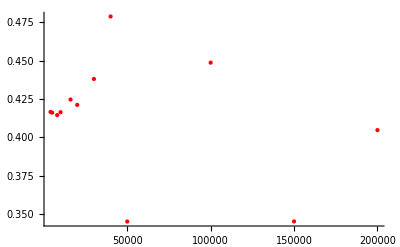

```mathematica
ListPlot[data,PlotStyle->Red,PlotRange->Full]
```

fit :  (0.0812201+0.374587/x^0.54)

0.997587 = r0

0.54 = z0

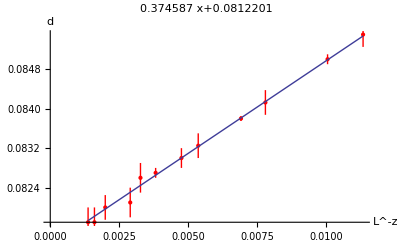

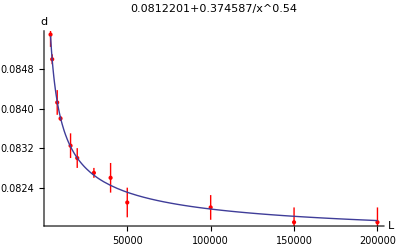

{0.0812201+0.374587/x^0.54, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0812201 | 0.000040313 | 2014.74 | 2.23312×10^-29
1/x^0.54 | 0.374587 | 0.0058264 | 64.2914 | 2.01725×10^-14}

FittedModel[-0.871009-0.551967 x]

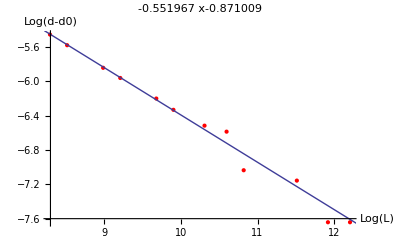

{-0.871009-0.551967 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.871009 | 0.160193 | -5.43723 | 0.00028596
x | -0.551967 | 0.0168793 | -32.7008 | 1.68652×10^-11}

```mathematica
ClearAll[z,r,x,k]
r0=0;
For[z=0.0,z<1.5,z+=0.01;
Maxxs=Table[{Maxx[[All,1]][[i]],Maxx[[All,2]][[i]]},{i,1,Length[Maxx]}];
model=k*x^-z+d;
fit=LinearModelFit[Maxxs,{1,x^-z},x,Weights->1/Errorx^2];
(*fit=NonlinearModelFit[Maxxs,model,{k,d},x,Weights->1/Errorx^2];*)

r=fit["RSquared"];
r
If[r>r0,
ffit=fit["BestFit"];
fitf=fit;
val=fit["ParameterTableEntries"];
r0=r;
z0=z;
]


]
ffit "fit : "
r0 "= r0"
z0 "= z0"
Maxxs=Table[{Maxx[[All,1]][[i]]^-z0,Maxx[[All,2]][[i]]},{i,1,Length[Maxx]}];
errx=Table[Errorx[[i]]*(z0)*Maxx[[All,1]][[i]]^(-z0-1),{i,1,Length[Errorx]}];
maxxerrs=Table[{Maxxs[[i]],ErrorBar[Errorx[[i]]]},{i,0,Length[Errorx]}];

(*pic1=ListPlot[Maxxs,PlotStyle->Red,AxesLabel->{"L^-z","d"},PlotLabel->ffit];*)
pic1=ErrorListPlot[maxxerrs,PlotStyle->Red,AxesLabel->{"L^-z","d"},PlotLabel->val[[1]][[1]]+val[[2]][[1]]*"x"];
pic2=Plot[val[[1]][[1]]+val[[2]][[1]]*x,{x,Maxx[[All,1]][[1]]^-z0,Maxx[[All,1]][[Length[Maxx]]]^-z0}];
Show[{pic1,pic2}]
maxyerr=Table[{Maxy[[i]],ErrorBar[Errory[[i]]]},{i,0,Length[Errory]}];
maxxerr=Table[{Maxx[[i]],ErrorBar[Errorx[[i]]]},{i,0,Length[Errorx]}];
pic1=ErrorListPlot[maxxerr,PlotRange->Full,PlotStyle->Red,AxesLabel->{"L","d"},PlotLabel->ffit];
pic3=Plot[val[[1]][[1]]+val[[2]][[1]]*x^-z0,{x,4000,200000},PlotRange->Full];
Show[{pic1,pic3}]
fitf[{"BestFit","ParameterTable"}]

ClearAll[k,x,z]
Maxxzcheck=Table[{Log[Maxx[[All,1]][[i]]],Log[Maxx[[All,2]][[i]]-val[[1]][[1]]]},{i,1,Length[Maxx]}];
Errorxzcheck=Table[Errorx[[i]]/Maxxzcheck[[All,2]][[i]],{i,1,Length[Maxx]}];
model=k-z*x;
fit=LinearModelFit[Maxxzcheck,{1,x},x,Weights->1/Errorx^2]
maxxzcheckerr=Table[{Maxxzcheck[[i]],ErrorBar[Errorxzcheck[[i]]]},{i,0,Length[Errorx]}];
ffit=fit["BestFit"];
fitf=fit;
val=fit["ParameterTableEntries"];
pic1=ErrorListPlot[maxxzcheckerr,PlotRange->Full,PlotStyle->Red,AxesLabel->{"Log(L)","Log(d-d0)"},PlotLabel->ffit];
pic3=Plot[val[[1]][[1]]+val[[2]][[1]]*x,{x,7,13},PlotRange->Full];
Show[{pic1,pic3}]
fitf[{"BestFit","ParameterTable"}]
```

```mathematica
-----------------------------------------------------------------------------------------
```

```mathematica
Maxx={{4000,0.0855},{5000,0.085},{8000,0.084125},{10000,0.0838},{16000,0.08325},{20000,0.083},{30000,0.0827},{40000,0.0826},{50000,0.0821},{100000,0.082},{150000,0.0817},{200000,0.0817}}
Maxy={{4000,21.65885},{5000,19.60315},{8000,15.959175},{10000,14.64014},{16000,11.476725},{20000,9.729393000000002},{30000,7.3744375},{40000,6.557308333333333},{50000,6.02102},{100000,4.6185275},{150000,2.5028900000000003},{200000,2.4837325}}
Errorx={0.00025,0.0001,0.00025,0.00005,0.00025,0.0002,0.0001,0.0003,0.0003,0.00025,0.0003,0.0003}
Errory={0.1,0.1,0.05,0.2,0.2,0.15,0.1,0.1,0.2,0.3,0.02,0.02}
```

```mathematica
ClearAll[Maxx,Maxy,Errorx,Errory]
ClearAll[Maxx,Maxy,Errorx,Errory]
Do[
Maxx1[v]={};
Maxy1[v]={};
Errorx1[v]={};
Errory1[v]={};
,{v,{4,5,6,7,8,11}}]
Do[
Do[
Maxd[v][l]=Sort[Ch4[v][l],#1[[2]]>#2[[2]]&];
Maxx1[v]=Append[Maxx1[v],{l*1000,Maxd[v][l][[All,1]][[1]]}];
Errorx1[v]=Append[Errorx1[v],Abs[Maxd[v][l][[All,1]][[3]]-Maxd[v][l][[All,1]][[2]]]/2];

Maxy1[v]=Append[Maxy1[v],{l*1000,Maxd[v][l][[All,2]][[1]]}];
Errory1[v]=Append[Errory1[v],Abs[Maxd[v][l][[All,2]][[1]]-Maxd[v][l][[All,2]][[2]]]];

,{l,{1,2,4,5,10,20}}]
,{v,{4}}]



Do[
Do[
Maxd[v][l]=Sort[Ch4[v][l],#1[[2]]>#2[[2]]&];
Maxx1[v]=Append[Maxx1[v],{l*1000,Maxd[v][l][[All,1]][[1]]}];
Errorx1[v]=Append[Errorx1[v],Abs[Maxd[v][l][[All,1]][[3]]-Maxd[v][l][[All,1]][[2]]]/2];

Maxy1[v]=Append[Maxy1[v],{l*1000,Maxd[v][l][[All,2]][[1]]}];
Errory1[v]=Append[Errory1[v],Abs[Maxd[v][l][[All,2]][[1]]-Maxd[v][l][[All,2]][[2]]]];

,{l,{2,5,10,20,40}}]
,{v,{5,6,7,8,11}}]
```

```mathematica
Maxd[v][10]
```

```mathematica
v=6
Maxx1[v]
Errorx1[v]
Maxy1[v]
Errory1[v]
```

6

{{2000,0.1225},{5000,0.1204},{10000,0.119},{20000,0.1185},{40000,0.118}}

{0.0005,0.0004,0.00075,0.00025,0.0005}

{{2000,6.39868},{5000,4.82902},{10000,3.80856},{20000,3.48583},{40000,3.12668}}

{0.19054,0.0361225,0.04616,0.0451975,0.0197575}

fit :  (0.06577+0.100367/x^0.33)

0.999843 = r0

0.33 = z0

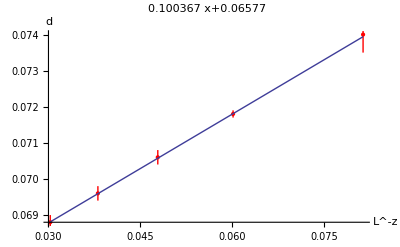

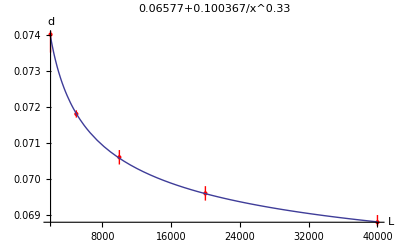

{0.06577+0.100367/x^0.33, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.06577 | 0.0000385184 | 1707.5 | 4.42988×10^-10
1/x^0.33 | 0.100367 | 0.000725227 | 138.393 | 8.31846×10^-7}

FittedModel[-2.29556-0.330373 x]

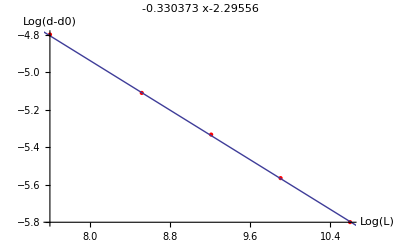

{-2.29556-0.330373 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | -2.29556 | 0.0188627 | -121.698 | 1.22325×10^-6
x | -0.330373 | 0.002051 | -161.079 | 5.27584×10^-7}

(14289. fit :)/x^0.87

0.997332 = r0

0.87 = α0

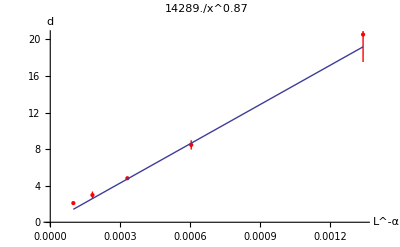

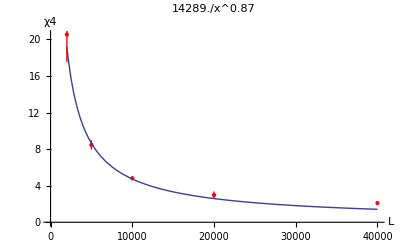

{14289./x^0.87, | Estimate | Standard Error | t-Statistic | P-Value
k | 14289. | 369.548 | 38.6662 | 2.67232×10^-6}

FittedModel[7.32461-0.621644 x]

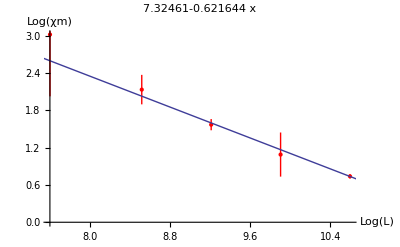

{7.32461-0.621644 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 7.32461 | 0.25965 | 28.2096 | 0.0000977957
x | -0.621644 | 0.0249522 | -24.9134 | 0.000141794}

```mathematica
v=11;
Maxx=Maxx1[v];
Errorx=Errorx1[v];
Maxy=Maxy1[v];
Errory=Errory1[v];
ClearAll[z,r,x,k,r0,fit,ffit]
r0=0;
For[z=0.0,z<2.5,z+=0.01;
Maxxs=Table[{Maxx[[All,1]][[i]],Maxx[[All,2]][[i]]},{i,1,Length[Maxx]}];
model=k*x^-z+d;
fit=LinearModelFit[Maxxs,{1,x^-z},x,Weights->1/Errorx^2];
(*fit=NonlinearModelFit[Maxxs,model,{k,d},x,Weights->1/Errorx^2];*)

r=fit["RSquared"];
r
If[r>r0,
ffit=fit["BestFit"];
fitf=fit;
val=fit["ParameterTableEntries"];
r0=r;
z0=z;
]


]
ffit "fit : "
r0 "= r0"
z0 "= z0"
Maxxs=Table[{Maxx[[All,1]][[i]]^-z0,Maxx[[All,2]][[i]]},{i,1,Length[Maxx]}];
errx=Table[Errorx[[i]]*(z0)*Maxx[[All,1]][[i]]^(-z0-1),{i,1,Length[Errorx]}];
maxxerrs=Table[{Maxxs[[i]],ErrorBar[Errorx[[i]]]},{i,0,Length[Errorx]}];

(*pic1=ListPlot[Maxxs,PlotStyle->Red,AxesLabel->{"L^-z","d"},PlotLabel->ffit];*)
pic1=ErrorListPlot[maxxerrs,PlotStyle->Red,AxesLabel->{"L^-z","d"},PlotLabel->val[[1]][[1]]+val[[2]][[1]]*"x"];
pic2=Plot[val[[1]][[1]]+val[[2]][[1]]*x,{x,Maxx[[All,1]][[1]]^-z0,Maxx[[All,1]][[Length[Maxx]]]^-z0}];
Show[{pic1,pic2}]
maxyerr=Table[{Maxy[[i]],ErrorBar[Errory[[i]]]},{i,0,Length[Errory]}];
maxxerr=Table[{Maxx[[i]],ErrorBar[Errorx[[i]]]},{i,0,Length[Errorx]}];
pic1=ErrorListPlot[maxxerr,PlotRange->Full,PlotStyle->Red,AxesLabel->{"L","d"},PlotLabel->ffit];
pic3=Plot[val[[1]][[1]]+val[[2]][[1]]*x^-z0,{x,2000,40000},PlotRange->Full];
Show[{pic1,pic3}]
fitf[{"BestFit","ParameterTable"}]

ClearAll[k,x,z]
Maxxzcheck=Table[{Log[Maxx[[All,1]][[i]]],Log[Maxx[[All,2]][[i]]-val[[1]][[1]]]},{i,1,Length[Maxx]}];
Errorxzcheck=Table[Errorx[[i]]/Maxxzcheck[[All,2]][[i]],{i,1,Length[Maxx]}];
model=k-z*x;
fit=LinearModelFit[Maxxzcheck,{1,x},x,Weights->1/Errorxzcheck^2]
maxxzcheckerr=Table[{Maxxzcheck[[i]],ErrorBar[Errorxzcheck[[i]]]},{i,0,Length[Errorx]}];
ffit=fit["BestFit"];
fitf=fit;
val=fit["ParameterTableEntries"];
pic1=ErrorListPlot[maxxzcheckerr,PlotRange->Full,PlotStyle->Red,AxesLabel->{"Log(L)","Log(d-d0)"},PlotLabel->ffit];
pic3=Plot[val[[1]][[1]]+val[[2]][[1]]*x,{x,7,13},PlotRange->Full];
Show[{pic1,pic3}]
fitf[{"BestFit","ParameterTable"}]



r0=0;
For[α=0.0,α<1,α+=0.01;
Maxys=Table[{Maxy[[All,1]][[i]],Maxy[[All,2]][[i]]},{i,1,Length[Maxy]}];
model=k*x^-α;
fit=NonlinearModelFit[Maxys,model,{k},x,Weights->1/Errorx^2];

r=fit["RSquared"];
If[r>r0,
ffit=fit["BestFit"];
val=fit["ParameterTableEntries"];
r0=r;
α0=α;
fitf=fit;
]


]
ffit "fit : "
r0 "= r0"
α0 "= α0"
Maxys=Table[{Maxy[[All,1]][[i]]^-α0,Maxy[[All,2]][[i]]},{i,1,Length[Maxy]}];
erry=Table[Errory[[i]]*(α0)*Maxy[[All,1]][[i]]^(-α0-1),{i,1,Length[Errory]}];
maxyerrs=Table[{Maxys[[i]],ErrorBar[Errory[[i]]]},{i,0,Length[Errory]}];

(*pic1=ListPlot[Maxxs,PlotStyle->Red,AxesLabel->{"L^-z","d"},PlotLabel->ffit];*)
pic1=ErrorListPlot[maxyerrs,PlotStyle->Red,AxesLabel->{"L^-α","d"},PlotLabel->ffit];

(*pic1=ListPlot[Maxys,PlotStyle->Red,AxesLabel->{"L^-α","χ4"},PlotLabel->ffit];*)
pic2=Plot[val[[1]][[1]]*x,{x,Maxy[[All,1]][[1]]^-α0,Maxy[[All,1]][[Length[Maxx]]]^-α0}];
Show[{pic1,pic2}]
maxyerr=Table[{Maxy[[i]],ErrorBar[Errory[[i]]]},{i,0,Length[Errory]}];
pic1=ErrorListPlot[maxyerr,PlotStyle->Red,AxesLabel->{"L","χ4"},PlotLabel->ffit];
pic3=Plot[val[[1]][[1]]*x^-α0,{x,2000,40000},PlotRange->Full];
Show[{pic1,pic3}]
fitf[{"BestFit","ParameterTable"}]



ClearAll[k,x,z]
Maxyαcheck=Table[{Log[Maxy[[All,1]][[i]]],Log[Maxy[[All,2]][[i]]]},{i,1,Length[Maxy]}];
Erroryαcheck=Table[Errory[[i]]/Maxyαcheck[[All,2]][[i]],{i,1,Length[Maxy]}];
model=k-z*x;
fit=LinearModelFit[Maxyαcheck,{1,x},x,Weights->1/Erroryαcheck^2]

maxvαcheckerr=Table[{Maxyαcheck[[i]],ErrorBar[Erroryαcheck[[i]]]},{i,0,Length[Erroryαcheck]}];
ffit=fit["BestFit"];
fitf=fit;
val=fit["ParameterTableEntries"];
pic1=ErrorListPlot[maxvαcheckerr,PlotRange->Full,PlotStyle->Red,AxesLabel->{"Log(L)","Log(χm)"},PlotLabel->ffit];
pic3=Plot[val[[1]][[1]]+val[[2]][[1]]*x,{x,7,13},PlotRange->Full];
Show[{pic1,pic3}]
fitf[{"BestFit","ParameterTable"}]
```

```mathematica
--------------------------------------------------------------------------------------
```

```mathematica
d0={{4,0.16640618474394098},{5,0.13868040135702742},{6,0.11675839124676939},{7,0.10129517685639909},{8,0.08925417883112817},{9,0.08122007942715888},{11,0.06576996509783684}};
errord0={0.00033616099689239286,0.00005787227492959545,0.00007991954500288723,0.00009054096014253667,0.0001526951489398501,0.0000403129906596808,0.00003851839142418456};
id0=Interpolation[d0];
d0f=Table[{d0[[i]],ErrorBar[errord0[[i]]]},{i,1,Length[d0]}]
z={{4,1.17},{5,0.8335917446127652},{6,0.515482520090487},{7,0.46313980302928304},{8,0.3708605421359231},{9,0.5570706817831086},{11,0.330373282657935}};
errorz={0.38157015933389465,0.12437999700979206,0.018249535457852732,0.020312190714286752,0.013559564836098069,0.017720884460999124,0.002050998641575505};
iz=Interpolation[z];
zf=Table[{z[[i]],ErrorBar[errorz[[i]]]},{i,1,Length[z]}]
α={{4,0.09021519670799975},{5,0.11176351761250464},{6,0.20594716719445325},{7,0.36868448770421297},{8,0.42632483220154554},{9,0.5887131541355719},{11,0.6216439922507675}};
errorα={0.010930520724000518,0.007669350297109258,0.020509584068115157,0.01646837484456931,0.05147229862991825,0.013821096244531046,0.024952203088136893};
iα=Interpolation[α];
αf=Table[{α[[i]],ErrorBar[errorα[[i]]]},{i,1,Length[α]}]
```

{{{4,0.166406},ErrorBar[0.000336161]},{{5,0.13868},ErrorBar[0.0000578723]},{{6,0.116758},ErrorBar[0.0000799195]},{{7,0.101295},ErrorBar[0.000090541]},{{8,0.0892542},ErrorBar[0.000152695]},{{9,0.0812201},ErrorBar[0.000040313]},{{11,0.06577},ErrorBar[0.0000385184]}}

{{{4,1.17},ErrorBar[0.38157]},{{5,0.833592},ErrorBar[0.12438]},{{6,0.515483},ErrorBar[0.0182495]},{{7,0.46314},ErrorBar[0.0203122]},{{8,0.370861},ErrorBar[0.0135596]},{{9,0.557071},ErrorBar[0.0177209]},{{11,0.330373},ErrorBar[0.002051]}}

{{{4,0.0902152},ErrorBar[0.0109305]},{{5,0.111764},ErrorBar[0.00766935]},{{6,0.205947},ErrorBar[0.0205096]},{{7,0.368684},ErrorBar[0.0164684]},{{8,0.426325},ErrorBar[0.0514723]},{{9,0.588713},ErrorBar[0.0138211]},{{11,0.621644},ErrorBar[0.0249522]}}

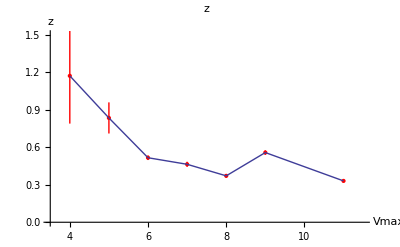

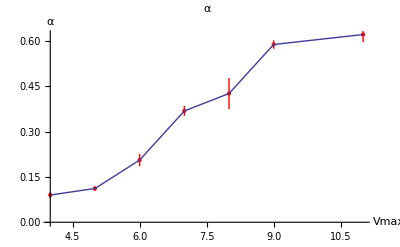

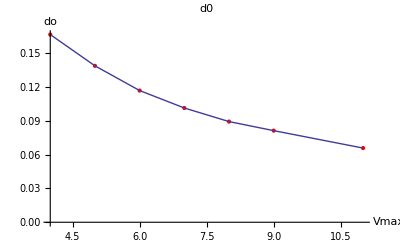

```mathematica
pic1=ErrorListPlot[zf,PlotRange->{{3.5,11.5},{0,1.5}},PlotLabel->"z",AxesLabel->{"Vmax","z"},PlotStyle->{Red}];
pic2=ListLinePlot[z];
Show[{pic1,pic2}]
pic3=ErrorListPlot[αf,PlotRange->{Full},PlotLabel->"α",AxesLabel->{"Vmax","α"},PlotStyle->Red];
pic4=ListLinePlot[α];
Show[{pic3,pic4}]
pic5=ErrorListPlot[d0f,PlotRange->{Full},PlotLabel->"d0",AxesLabel->{"Vmax","do"},PlotStyle->Red];
pic6=ListLinePlot[d0];
Show[{pic5,pic6}]
```